### the equilibrium of a promoter and transcription factor binding reactions

reactions:
1.  D+ T ⇄ TD
2.  D+T ⇄ DT
3.  TD+ T ⇄ TDT
 4.  DT +T ⇄ TDT

```mathematica
eqsol=Solve[{K1==(D T)/TD,K2==(D T)/DT,K3==(TD T)/TDT,Dtot==D+TD+DT+TDT},{D,DT,TD,TDT}]
```

{{D→(Dtot K1 K2 K3)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),DT→(Dtot K1 K3 T)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),TD→(Dtot K2 K3 T)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),TDT→(Dtot K2 T^2)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2)}}

```mathematica
param={K1->1,K2->2,K3->5,Dtot->1};
```

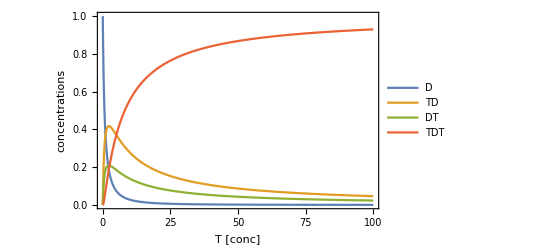

```mathematica
Plot[Evaluate[{D,TD,DT,TDT}/.eqsol/.param],{T,0,100},PlotLegends->{"D","TD","DT","TDT"},Frame->True,FrameLabel->{"T [conc]","concentrations"}]
```

```mathematica
Manipulate[Plot[{(K1 K2 K3)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),(K1 K3 T)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),(K2 K3 T)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2),(K2 T^2)/(K1 K2 K3+K1 K3 T+K2 K3 T+K2 T^2)},{T,0,50},PlotLegends->{"D/D_T","TD/D_T","DT/D_T","TDT/D_T"},Frame->True,BaseStyle->FontSize->14,FrameLabel->{"T [conc]","promoter fractions"},PlotRange->{{0,50},{0,1}}],
{{K1,1,"dissociation constant reaction 1 (K_1)"},0.1,10,Appearance->"Open"},
{{K2,2,"dissociation constant reaction 2 (K_2)"},0.1,10,Appearance->"Open"},
{{K3,5,"dissociation constant reaction 3 (K_3)"},0.1,10,Appearance->"Open"}]
```